```mathematica
x[t_]:= 3(t-2)^2
y[t_]:= 4+9 t^2
```

```mathematica
sol=Solve[x==3(t-2)^2,t]
```

{{t→1/3 (6-√3 √x)},{t→1/3 (6+√3 √x)}}

```mathematica
y[t]/.sol
```

{4+(6-√3 √x)^2,4+(6+√3 √x)^2}

```mathematica
sol1=D[y[t]/.sol, x]//FullSimplify
```

{3-(6 √3)/(√x),3+(6 √3)/(√x)}

```mathematica
sol2=D[y[t]/.sol, {x,2}]//FullSimplify
```

{(3 √3)/x^(3/2),-(3 √3)/x^(3/2)}

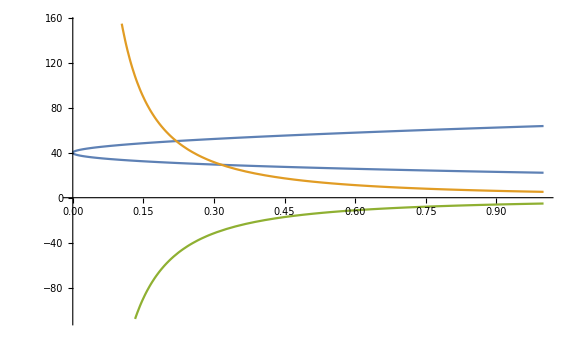

{(3 √3)/x^(3/2),-(3 √3)/x^(3/2)}

```mathematica
Plot[{y[t]/.sol, sol2}, {x, 0, 1}, ImageSize->Large]
```

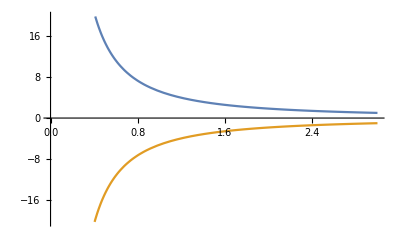

```mathematica
Plot[sol2,{x, 0, 3}]
```